```mathematica
(*propfac=0.4*)
J2Prop=Simplify[Sqrt[J2Sig]/.{sig2->sig1 propfac,sig3->sig1 propfac},Assumptions->{sig1<0,propfac>0,propfac<1}]
I1Prop=I1Sig/.{sig2->sig1 propfac,sig3->sig1 propfac}
Solve[{J2Prop==J2Val,I1Prop==I1Val},{sig1,propfac}]
Clear[propfac]
```

((-1+propfac) sig1)/(√3)

sig1+2 propfac sig1

{{sig1→1/3 (I1Val-2 √3 J2Val),propfac→(√3 I1Val+3 J2Val)/(√3 I1Val-6 J2Val)}}

```mathematica
propfac=0.6
J2Prop=Simplify[Sqrt[J2Sig]/.{sig2->sig1 propfac,sig3->sig1 propfac},Assumptions->{sig1<0,propfac>0,propfac<1}]
I1Prop=I1Sig/.{sig2->sig1 propfac,sig3->sig1 propfac}
Clear[propfac]
```

0.6

-0.23094 sig1

2.2 sig1

```mathematica
IJ2=Table[{I1Prop,J2Prop,sig1},{sig1,0,-0.86,-0.86/40}]
IJ2AdjustEpsp[IJ_]:=Block[{lij,f2,epsp,i,tabepsp},
lij=Length[IJ];
tabepsp=Table[0,{lij}];
epsp=0;

For[i=1,i≤lij,i++,
f2=Function2[IJ[[i,1]],IJ[[i,2]],epsp];
If[f2>0,
epsp=SolveFunction2Epsp[IJ[[i,1]],IJ[[i,2]],epsp];
tabepsp[[i]]=epsp
,tabepsp[[i]]=epsp]
];
tabepsp
]
Table[{Function1[IJ2[[i,1]],IJ2[[i,2]]],Function2[IJ2[[i,1]],IJ2[[i,2]],0]},{i,1,Length[IJ2]}]
TabEpsp=IJ2AdjustEpsp[IJ2]
```

{{0.,0.,0.},{-0.0473,0.00496521,-0.0215},{-0.0946,0.00993042,-0.043},{-0.1419,0.0148956,-0.0645},{-0.1892,0.0198608,-0.086},{-0.2365,0.0248261,-0.1075},{-0.2838,0.0297913,-0.129},{-0.3311,0.0347565,-0.1505},{-0.3784,0.0397217,-0.172},{-0.4257,0.0446869,-0.1935},{-0.473,0.0496521,-0.215},{-0.5203,0.0546173,-0.2365},{-0.5676,0.0595825,-0.258},{-0.6149,0.0645478,-0.2795},{-0.6622,0.069513,-0.301},{-0.7095,0.0744782,-0.3225},{-0.7568,0.0794434,-0.344},{-0.8041,0.0844086,-0.3655},{-0.8514,0.0893738,-0.387},{-0.8987,0.094339,-0.4085},{-0.946,0.0993042,-0.43},{-0.9933,0.104269,-0.4515},{-1.0406,0.109235,-0.473},{-1.0879,0.1142,-0.4945},{-1.1352,0.119165,-0.516},{-1.1825,0.12413,-0.5375},{-1.2298,0.129096,-0.559},{-1.2771,0.134061,-0.5805},{-1.3244,0.139026,-0.602},{-1.3717,0.143991,-0.6235},{-1.419,0.148956,-0.645},{-1.4663,0.153922,-0.6665},{-1.5136,0.158887,-0.688},{-1.5609,0.163852,-0.7095},{-1.6082,0.168817,-0.731},{-1.6555,0.173782,-0.7525},{-1.7028,0.178748,-0.774},{-1.7501,0.183713,-0.7955},{-1.7974,0.188678,-0.817},{-1.8447,0.193643,-0.8385},{-1.892,0.198608,-0.86}}

{{-0.07,4.52971×10^-14},{-0.0706497,0.846137},{-0.0711243,1.96247},{-0.0714292,3.349},{-0.0715697,5.00573},{-0.0715509,6.93266},{-0.0713778,9.12979},{-0.0710552,11.5971},{-0.0705879,14.3346},{-0.0699802,17.3423},{-0.0692365,20.6203},{-0.0683612,24.1684},{-0.0673583,27.9867},{-0.0662318,32.0752},{-0.0649856,36.4339},{-0.0636234,41.0628},{-0.0621487,45.9619},{-0.0605652,51.1312},{-0.0588762,56.5707},{-0.057085,62.2804},{-0.0551947,68.2603},{-0.0532086,74.5104},{-0.0511295,81.0307},{-0.0489604,87.8211},{-0.0467041,94.8818},{-0.0443633,102.213},{-0.0419406,109.814},{-0.0394386,117.685},{-0.0368597,125.827},{-0.0342064,134.238},{-0.031481,142.92},{-0.0286858,151.872},{-0.0258228,161.094},{-0.0228943,170.587},{-0.0199022,180.35},{-0.0168486,190.382},{-0.0137353,200.685},{-0.0105643,211.259},{-0.00733733,222.102},{-0.00405612,233.216},{-0.000722377,244.6}}

{-1.31941×10^-16,-0.00208164,-0.00413556,-0.00615331,-0.00812945,-0.0100605,-0.0119444,-0.0137798,-0.0155662,-0.0173036,-0.0189922,-0.0206326,-0.0222254,-0.0237714,-0.0252718,-0.0267274,-0.0281393,-0.0295088,-0.0308369,-0.0321248,-0.0333737,-0.0345848,-0.0357593,-0.0368984,-0.0380033,-0.0390753,-0.0401156,-0.0411254,-0.0421061,-0.0430591,-0.0439857,-0.0448876,-0.0457664,-0.0466242,-0.0474633,-0.0482867,-0.0490986,-0.0499054,-0.0507181,-0.051561,-0.0525244}

### Compute the derivatives of the Plastic deformation and Total deformation

```mathematica
Derivatives[IJ_,DerivIJ_,epsp_]:=Block[{gradf2,lval,flval,df2depsp,dlval,dfval,derivT,epspponto,gammaponto,trN2,deformPlast,deformElast,deformTotal,ST,pr},
pr=True;
lval=LFunction[epsp];
If[pr,Print["lval = ",lval]];
flval=F[lval]/.exemple;
If[pr,Print["flval = ",flval]];
gradf2={2(IJ[[1]]-lval)√3/(flval R)^2,√2 IJ[[2]]/flval^2}/.exemple;
If[pr,Print["gradf2 = ",gradf2]];
derivT={(1/√3 )DerivIJ[[1]],DerivIJ[[2]]√2};
If[pr,Print["derivT = ",derivT]];
dlval=DLFunction[epsp];
If[pr,Print["dlval = ",dlval]];
If[pr,Print["B lval = ",B lval/.exemple]];
If[pr,Print["- C B E^(B lval) = ",-C B E^(B lval)/.exemple]];
dfval=-C B E^(B lval)dlval/.exemple;
If[pr,Print["dfval = ",dfval]];
If[pr,Print["one = ",2(lval-IJ[[1]])dlval/(flval R)^2/.exemple]];
If[pr,Print["two = ",- 2(lval-IJ[[1]])^2 dfval/(flval^3 R^2)/.exemple]];
If[pr,Print["three = ",-2 IJ[[2]]^2 dfval/flval^3/.exemple]];
If[pr,Print["four = ",-2 IJ[[2]]^2 dfval/.exemple]];

df2depsp=2(lval-IJ[[1]])dlval/(flval R)^2 - 2(lval-IJ[[1]])^2 dfval/(flval^3 R^2)-2 IJ[[2]]^2 dfval/flval^3/.exemple;
If[pr,Print["df2depsp = ",df2depsp]];
epspponto=-(gradf2.derivT)/df2depsp/.exemple;
If[pr,Print["epspponto = ",epspponto]];
trN2=6(IJ[[1]]-lval)/(flval R)^2/.exemple;
If[pr,Print["trN2 = ",trN2]];
gammaponto=epspponto/trN2;
If[pr,Print["gammaponto = " ,gammaponto]];
deformPlast=gammaponto gradf2;
If[pr,Print["deformPlast = ",deformPlast]];
ST={0,1};
If[pr,Print["ST = ",ST]];
deformElast={1/K 1/√3 derivT[[1]],(1/(2 G))(ST.derivT)}/.exemple;
If[pr,Print["deformElast = ",deformElast]];
deformTotal=deformElast+deformPlast;
{deformTotal,deformPlast,epspponto}

]
Derivatives[IJ2[[-2]],(IJ2[[2]]-IJ2[[1]]),TabEpsp[[-2]]]
Derivatives[IJ2[[-1]],(IJ2[[2]]-IJ2[[1]]),TabEpsp[[-1]]]
```

lval = -1.77981

flval = 0.195375

gradf2 = {-0.942261,7.17428}

derivT = {-0.0273087,0.00702187}

dlval = 94.7037

B lval = -1.19247

- C B E^(B lval) = -0.0365986

dfval = -3.46602

one = 51.5202

two = 0.626285

three = 34.8543

four = 0.259935

df2depsp = 87.0008

epspponto = -0.000874805

trN2 = -1.63204

gammaponto = 0.000536018

deformPlast = {-0.000505069,0.00384554}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

{{-0.000741569,0.00393331},{-0.000505069,0.00384554},-0.000874805}

lval = -1.87447

flval = 0.198732

gradf2 = {-0.246015,7.11174}

derivT = {-0.0273087,0.00702187}

dlval = 101.999

B lval = -1.25589

- C B E^(B lval) = -0.0343494

dfval = -3.50361

one = 14.4876

two = 0.0438972

three = 35.2157

four = 0.276402

df2depsp = 49.7473

epspponto = -0.00113888

trN2 = -0.426111

gammaponto = 0.00267273

deformPlast = {-0.000657532,0.0190078}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

{{-0.000894032,0.0190955},{-0.000657532,0.0190078},-0.00113888}

```mathematica
Length[AllDeriv]
Length[IJ2]
```

0

41

```mathematica
AllDeriv=Table[Derivatives[IJ2[[i]],(IJ2[[2]]-IJ2[[1]]),TabEpsp[[i]]],{i,1,Length[IJ2]}]
FirstDeform={{{IJ2[[1,1]]/(K√3),IJ2[[1,2]]/(2 G)},{0,0},TabEpsp[[1]]}}/.exemple
For[i=1,i<Length[AllDeriv],i++,
AppendTo[FirstDeform,FirstDeform[[i]]+(AllDeriv[[i]]+AllDeriv[[i+1]])/2]
]
```

lval = 0.133045

flval = 0.0532179

gradf2 = {-26.0371,0.}

derivT = {-0.0273087,0.00702187}

dlval = 17.0081

dfval = -2.24242

df2depsp = 339.949

epspponto = -0.00209161

trN2 = -45.0976

gammaponto = 0.0000463796

deformPlast = {-0.00120759,0.}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = 0.0969623

flval = 0.0579181

gradf2 = {-23.836,2.09326}

derivT = {-0.0273087,0.00702187}

dlval = 17.6667

dfval = -2.27361

df2depsp = 321.635

epspponto = -0.00206952

trN2 = -41.2852

gammaponto = 0.0000501273

deformPlast = {-0.00119484,0.000104929}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = 0.0599699

flval = 0.0626204

gradf2 = {-21.8476,3.58139}

derivT = {-0.0273087,0.00702187}

dlval = 18.3626

dfval = -2.30532

df2depsp = 305.25

epspponto = -0.00203695

trN2 = -37.8412

gammaponto = 0.0000538288

deformPlast = {-0.00117603,0.000192782}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = 0.0221878

flval = 0.0673042

gradf2 = {-20.0772,4.6504}

derivT = {-0.0273087,0.00702187}

dlval = 19.0958

dfval = -2.33744

df2depsp = 290.809

epspponto = -0.00199766

trN2 = -34.7747

gammaponto = 0.0000574456

deformPlast = {-0.00115335,0.000267145}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.0163003

flval = 0.0719551

gradf2 = {-18.5089,5.42487}

derivT = {-0.0273087,0.00702187}

dlval = 19.8663

dfval = -2.36986

df2depsp = 278.165

epspponto = -0.00195405

trN2 = -32.0584

gammaponto = 0.0000609527

deformPlast = {-0.00112817,0.000330661}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.0554349

flval = 0.0765628

gradf2 = {-17.1202,5.98945}

derivT = {-0.0273087,0.00702187}

dlval = 20.675

dfval = -2.4025

df2depsp = 267.119

epspponto = -0.00190772

trN2 = -29.6531

gammaponto = 0.0000643346

deformPlast = {-0.00110142,0.000385329}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.0951725

flval = 0.0811195

gradf2 = {-15.8878,6.40256}

derivT = {-0.0273087,0.00702187}

dlval = 21.5229

dfval = -2.43531

df2depsp = 257.468

epspponto = -0.00185978

trN2 = -27.5186

gammaponto = 0.0000675826

deformPlast = {-0.00107374,0.000432702}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.135481

flval = 0.0856194

gradf2 = {-14.7903,6.70512}

derivT = {-0.0273087,0.00702187}

dlval = 22.411

dfval = -2.46824

df2depsp = 249.028

epspponto = -0.00181099

trN2 = -25.6175

gammaponto = 0.0000706933

deformPlast = {-0.00104557,0.000474007}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.176338

flval = 0.0900581

gradf2 = {-13.8086,6.92623}

derivT = {-0.0273087,0.00702187}

dlval = 23.3409

dfval = -2.50124

df2depsp = 241.63

epspponto = -0.00176191

trN2 = -23.9172

gammaponto = 0.0000736669

deformPlast = {-0.00101724,0.000510234}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.217725

flval = 0.0944323

gradf2 = {-12.9265,7.08686}

derivT = {-0.0273087,0.00702187}

dlval = 24.3142

dfval = -2.53428

df2depsp = 235.133

epspponto = -0.00171293

trN2 = -22.3893

gammaponto = 0.000076507

deformPlast = {-0.000988963,0.000542194}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.259632

flval = 0.0987395

gradf2 = {-12.1299,7.2023}

derivT = {-0.0273087,0.00702187}

dlval = 25.3326

dfval = -2.56732

df2depsp = 229.411

epspponto = -0.00166437

trN2 = -21.0097

gammaponto = 0.0000792194

deformPlast = {-0.000960925,0.000570561}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.302049

flval = 0.102978

gradf2 = {-11.4072,7.28381}

derivT = {-0.0273087,0.00702187}

dlval = 26.398

dfval = -2.60034

df2depsp = 224.36

epspponto = -0.00161643

trN2 = -19.7579

gammaponto = 0.000081812

deformPlast = {-0.000933248,0.000595903}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.344972

flval = 0.107146

gradf2 = {-10.7483,7.33981}

derivT = {-0.0273087,0.00702187}

dlval = 27.5127

dfval = -2.6333

df2depsp = 219.885

epspponto = -0.00156928

trN2 = -18.6167

gammaponto = 0.0000842945

deformPlast = {-0.000906026,0.000618706}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.388399

flval = 0.111242

gradf2 = {-10.1447,7.3766}

derivT = {-0.0273087,0.00702187}

dlval = 28.6788

dfval = -2.6662

df2depsp = 215.909

epspponto = -0.00152304

trN2 = -17.5712

gammaponto = 0.0000866781

deformPlast = {-0.000879326,0.00063939}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.43233

flval = 0.115267

gradf2 = {-9.58921,7.39897}

derivT = {-0.0273087,0.00702187}

dlval = 29.8988

dfval = -2.699

df2depsp = 212.36

epspponto = -0.00147779

trN2 = -16.609

gammaponto = 0.0000889752

deformPlast = {-0.000853202,0.000658325}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.476768

flval = 0.119219

gradf2 = {-9.07555,7.41056}

derivT = {-0.0273087,0.00702187}

dlval = 31.1753

dfval = -2.73168

df2depsp = 209.178

epspponto = -0.0014336

trN2 = -15.7193

gammaponto = 0.0000911999

deformPlast = {-0.000827689,0.000675843}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.521718

flval = 0.123099

gradf2 = {-8.59843,7.41417}

derivT = {-0.0273087,0.00702187}

dlval = 32.5113

dfval = -2.76423

df2depsp = 206.307

epspponto = -0.00139052

trN2 = -14.8929

gammaponto = 0.0000933677

deformPlast = {-0.000802816,0.000692244}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.567186

flval = 0.126907

gradf2 = {-8.15327,7.41195}

derivT = {-0.0273087,0.00702187}

dlval = 33.9097

dfval = -2.79662

df2depsp = 203.697

epspponto = -0.00134858

trN2 = -14.1219

gammaponto = 0.0000954956

deformPlast = {-0.000778601,0.000707808}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.613181

flval = 0.130642

gradf2 = {-7.73605,7.40556}

derivT = {-0.0273087,0.00702187}

dlval = 35.374

dfval = -2.82885

df2depsp = 201.302

epspponto = -0.0013078

trN2 = -13.3992

gammaponto = 0.0000976026

deformPlast = {-0.000755059,0.000722802}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.659714

flval = 0.134306

gradf2 = {-7.3433,7.39631}

derivT = {-0.0273087,0.00702187}

dlval = 36.9076

dfval = -2.86089

df2depsp = 199.078

epspponto = -0.0012682

trN2 = -12.719

gammaponto = 0.0000997096

deformPlast = {-0.000732197,0.000737483}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.706799

flval = 0.137899

gradf2 = {-6.97193,7.38519}

derivT = {-0.0273087,0.00702187}

dlval = 38.5146

dfval = -2.89274

df2depsp = 196.985

epspponto = -0.0012298

trN2 = -12.0757

gammaponto = 0.00010184

deformPlast = {-0.000710024,0.000752111}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.75445

flval = 0.141421

gradf2 = {-6.6192,7.37297}

derivT = {-0.0273087,0.00702187}

dlval = 40.199

dfval = -2.92439

df2depsp = 194.982

epspponto = -0.00119259

trN2 = -11.4648

gammaponto = 0.000104022

deformPlast = {-0.000688543,0.000766952}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.802688

flval = 0.144874

gradf2 = {-6.28267,7.36025}

derivT = {-0.0273087,0.00702187}

dlval = 41.9657

dfval = -2.95582

df2depsp = 193.027

epspponto = -0.00115659

trN2 = -10.8819

gammaponto = 0.000106286

deformPlast = {-0.000667759,0.00078229}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.851533

flval = 0.148259

gradf2 = {-5.96013,7.34748}

derivT = {-0.0273087,0.00702187}

dlval = 43.8195

dfval = -2.98702

df2depsp = 191.081

epspponto = -0.00112181

trN2 = -10.3233

gammaponto = 0.000108668

deformPlast = {-0.000647676,0.000798436}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.901011

flval = 0.151577

gradf2 = {-5.64954,7.335}

derivT = {-0.0273087,0.00702187}

dlval = 45.7662

dfval = -3.01799

df2depsp = 189.1

epspponto = -0.00108824

trN2 = -9.7853

gammaponto = 0.000111212

deformPlast = {-0.000628298,0.000815742}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -0.951153

flval = 0.154828

gradf2 = {-5.34902,7.32307}

derivT = {-0.0273087,0.00702187}

dlval = 47.8119

dfval = -3.04873

df2depsp = 187.038

epspponto = -0.00105592

trN2 = -9.26478

gammaponto = 0.000113971

deformPlast = {-0.000609634,0.000834618}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.00199

flval = 0.158015

gradf2 = {-5.05679,7.31184}

derivT = {-0.0273087,0.00702187}

dlval = 49.9635

dfval = -3.07923

df2depsp = 184.844

epspponto = -0.00102485

trN2 = -8.75862

gammaponto = 0.00011701

deformPlast = {-0.000591696,0.00085556}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.05358

flval = 0.16114

gradf2 = {-4.77114,7.30144}

derivT = {-0.0273087,0.00702187}

dlval = 52.2287

dfval = -3.10949

df2depsp = 182.464

epspponto = -0.000995064

trN2 = -8.26385

gammaponto = 0.000120412

deformPlast = {-0.000574501,0.000879179}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.10596

flval = 0.164204

gradf2 = {-4.49037,7.2919}

derivT = {-0.0273087,0.00702187}

dlval = 54.6165

dfval = -3.13952

df2depsp = 179.833

epspponto = -0.000966611

trN2 = -7.77755

gammaponto = 0.000124282

deformPlast = {-0.000558073,0.000906254}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.15919

flval = 0.16721

gradf2 = {-4.21278,7.28323}

derivT = {-0.0273087,0.00702187}

dlval = 57.1368

dfval = -3.16932

df2depsp = 176.879

epspponto = -0.000939553

trN2 = -7.29676

gammaponto = 0.000128763

deformPlast = {-0.000542451,0.000937811}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.21335

flval = 0.170161

gradf2 = {-3.9366,7.27536}

derivT = {-0.0273087,0.00702187}

dlval = 59.8014

dfval = -3.1989

df2depsp = 173.515

epspponto = -0.000913984

trN2 = -6.81838

gammaponto = 0.000134047

deformPlast = {-0.000527689,0.00097524}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.26854

flval = 0.173059

gradf2 = {-3.65987,7.26817}

derivT = {-0.0273087,0.00702187}

dlval = 62.6241

dfval = -3.22829

df2depsp = 169.635

epspponto = -0.000890043

trN2 = -6.33909

gammaponto = 0.000140406

deformPlast = {-0.000513866,0.00102049}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.32487

flval = 0.175909

gradf2 = {-3.38044,7.2615}

derivT = {-0.0273087,0.00702187}

dlval = 65.6216

dfval = -3.25752

df2depsp = 165.11

epspponto = -0.000867935

trN2 = -5.85509

gammaponto = 0.000148236

deformPlast = {-0.000501103,0.00107642}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.38251

flval = 0.178716

gradf2 = {-3.09572,7.25507}

derivT = {-0.0273087,0.00702187}

dlval = 68.8144

dfval = -3.28661

df2depsp = 159.773

epspponto = -0.000847977

trN2 = -5.36194

gammaponto = 0.000158147

deformPlast = {-0.00048958,0.00114737}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.44166

flval = 0.181486

gradf2 = {-2.80251,7.24849}

derivT = {-0.0273087,0.00702187}

dlval = 72.2287

dfval = -3.31564

df2depsp = 153.407

epspponto = -0.000830671

trN2 = -4.85409

gammaponto = 0.000171128

deformPlast = {-0.000479588,0.00124042}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.50262

flval = 0.184228

gradf2 = {-2.49659,7.24122}

derivT = {-0.0273087,0.00702187}

dlval = 75.899

dfval = -3.34468

df2depsp = 145.712

epspponto = -0.000816856

trN2 = -4.32421

gammaponto = 0.000188903

deformPlast = {-0.000471612,0.00136789}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.56584

flval = 0.186955

gradf2 = {-2.17192,7.23237}

derivT = {-0.0273087,0.00702187}

dlval = 79.8739

dfval = -3.37388

df2depsp = 136.252

epspponto = -0.000808042

trN2 = -3.76188

gammaponto = 0.000214797

deformPlast = {-0.000466523,0.00155349}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.632

flval = 0.189689

gradf2 = {-1.81913,7.22055}

derivT = {-0.0273087,0.00702187}

dlval = 84.2267

dfval = -3.40346

df2depsp = 124.346

epspponto = -0.000807263

trN2 = -3.15083

gammaponto = 0.000256206

deformPlast = {-0.000466073,0.00184995}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.70239

flval = 0.192467

gradf2 = {-1.42153,7.20315}

derivT = {-0.0273087,0.00702187}

dlval = 89.0824

dfval = -3.43385

df2depsp = 108.794

epspponto = -0.000821732

trN2 = -2.46216

gammaponto = 0.000333744

deformPlast = {-0.000474427,0.00240401}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.77981

flval = 0.195375

gradf2 = {-0.942261,7.17428}

derivT = {-0.0273087,0.00702187}

dlval = 94.7037

dfval = -3.46602

df2depsp = 87.0008

epspponto = -0.000874805

trN2 = -1.63204

gammaponto = 0.000536018

deformPlast = {-0.000505069,0.00384554}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

lval = -1.87447

flval = 0.198732

gradf2 = {-0.246015,7.11174}

derivT = {-0.0273087,0.00702187}

dlval = 101.999

dfval = -3.50361

df2depsp = 49.7473

epspponto = -0.00113888

trN2 = -0.426111

gammaponto = 0.00267273

deformPlast = {-0.000657532,0.0190078}

ST = {0,1}

deformElast = {-0.0002365,0.0000877734}

{{{-0.00144409,0.0000877734},{-0.00120759,0.},-0.00209161},{{-0.00143134,0.000192703},{-0.00119484,0.000104929},-0.00206952},{{-0.00141253,0.000280555},{-0.00117603,0.000192782},-0.00203695},{{-0.00138985,0.000354919},{-0.00115335,0.000267145},-0.00199766},{{-0.00136467,0.000418434},{-0.00112817,0.000330661},-0.00195405},{{-0.00133792,0.000473102},{-0.00110142,0.000385329},-0.00190772},{{-0.00131024,0.000520475},{-0.00107374,0.000432702},-0.00185978},{{-0.00128207,0.00056178},{-0.00104557,0.000474007},-0.00181099},{{-0.00125374,0.000598007},{-0.00101724,0.000510234},-0.00176191},{{-0.00122546,0.000629967},{-0.000988963,0.000542194},-0.00171293},{{-0.00119743,0.000658335},{-0.000960925,0.000570561},-0.00166437},{{-0.00116975,0.000683677},{-0.000933248,0.000595903},-0.00161643},{{-0.00114253,0.000706479},{-0.000906026,0.000618706},-0.00156928},{{-0.00111583,0.000727163},{-0.000879326,0.00063939},-0.00152304},{{-0.0010897,0.000746098},{-0.000853202,0.000658325},-0.00147779},{{-0.00106419,0.000763616},{-0.000827689,0.000675843},-0.0014336},{{-0.00103932,0.000780017},{-0.000802816,0.000692244},-0.00139052},{{-0.0010151,0.000795582},{-0.000778601,0.000707808},-0.00134858},{{-0.000991559,0.000810575},{-0.000755059,0.000722802},-0.0013078},{{-0.000968697,0.000825257},{-0.000732197,0.000737483},-0.0012682},{{-0.000946524,0.000839884},{-0.000710024,0.000752111},-0.0012298},{{-0.000925043,0.000854725},{-0.000688543,0.000766952},-0.00119259},{{-0.000904259,0.000870063},{-0.000667759,0.00078229},-0.00115659},{{-0.000884176,0.000886209},{-0.000647676,0.000798436},-0.00112181},{{-0.000864798,0.000903515},{-0.000628298,0.000815742},-0.00108824},{{-0.000846134,0.000922392},{-0.000609634,0.000834618},-0.00105592},{{-0.000828196,0.000943333},{-0.000591696,0.00085556},-0.00102485},{{-0.000811001,0.000966952},{-0.000574501,0.000879179},-0.000995064},{{-0.000794573,0.000994027},{-0.000558073,0.000906254},-0.000966611},{{-0.000778951,0.00102558},{-0.000542451,0.000937811},-0.000939553},{{-0.000764189,0.00106301},{-0.000527689,0.00097524},-0.000913984},{{-0.000750366,0.00110827},{-0.000513866,0.00102049},-0.000890043},{{-0.000737603,0.00116419},{-0.000501103,0.00107642},-0.000867935},{{-0.00072608,0.00123514},{-0.00048958,0.00114737},-0.000847977},{{-0.000716088,0.00132819},{-0.000479588,0.00124042},-0.000830671},{{-0.000708112,0.00145566},{-0.000471612,0.00136789},-0.000816856},{{-0.000703023,0.00164127},{-0.000466523,0.00155349},-0.000808042},{{-0.000702573,0.00193772},{-0.000466073,0.00184995},-0.000807263},{{-0.000710927,0.00249178},{-0.000474427,0.00240401},-0.000821732},{{-0.000741569,0.00393331},{-0.000505069,0.00384554},-0.000874805},{{-0.000894032,0.0190955},{-0.000657532,0.0190078},-0.00113888}}

{{{0.,0.},{0,0},-1.31941×10^-16}}

{-1.31941×10^-16,-0.00208056,-0.00413379,-0.00615109,-0.00812695,-0.0100578,-0.0119416,-0.013777,-0.0155634,-0.0173008,-0.0189895,-0.0206299,-0.0222227,-0.0237689,-0.0252693,-0.026725,-0.0281371,-0.0295066,-0.0308348,-0.0321228,-0.0333718,-0.034583,-0.0357576,-0.0368968,-0.0380018,-0.0390739,-0.0401143,-0.0411242,-0.0421051,-0.0430582,-0.0439849,-0.0448869,-0.0457659,-0.0466239,-0.0474632,-0.048287,-0.0490994,-0.0499071,-0.0507216,-0.0515698,-0.0525767}

{-1.31941×10^-16,-0.00208164,-0.00413556,-0.00615331,-0.00812945,-0.0100605,-0.0119444,-0.0137798,-0.0155662,-0.0173036,-0.0189922,-0.0206326,-0.0222254,-0.0237714,-0.0252718,-0.0267274,-0.0281393,-0.0295088,-0.0308369,-0.0321248,-0.0333737,-0.0345848,-0.0357593,-0.0368984,-0.0380033,-0.0390753,-0.0401156,-0.0411254,-0.0421061,-0.0430591,-0.0439857,-0.0448876,-0.0457664,-0.0466242,-0.0474633,-0.0482867,-0.0490986,-0.0499054,-0.0507181,-0.051561,-0.0525244}

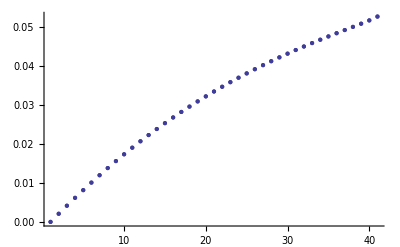

```mathematica
epsp=Table[FirstDeform[[i,3]],{i,Length[FirstDeform]}]
TabEpsp
ga=ListPlot[-epsp];
gb=ListPlot[-TabEpsp];
Show[ga,gb]
Clear[ga,gb]
```

```mathematica
Length[FirstDeform]
Length[IJ2]
```

41

41

```mathematica
FirstDeform
epssig=Table[{1/3(√3FirstDeform[[i,1,1]]-√2√3 FirstDeform[[i,1,2]]),IJ2[[i,3]]},{i,1,Length[FirstDeform]}]
```

{{{0.,0.},{0,0},-1.31941×10^-16},{{-0.00143771,0.000140238},{-0.00120121,0.0000524647},-0.00208056},{{-0.00285965,0.000376867},{-0.00238665,0.00020132},-0.00413379},{{-0.00426084,0.000694604},{-0.00355134,0.000431284},-0.00615109},{{-0.00563809,0.00108128},{-0.00469209,0.000730187},-0.00812695},{{-0.00698939,0.00152705},{-0.00580689,0.00108818},-0.0100578},{{-0.00831347,0.00202384},{-0.00689447,0.0014972},-0.0119416},{{-0.00960963,0.00256497},{-0.00795413,0.00195055},-0.013777},{{-0.0108775,0.00314486},{-0.00898554,0.00244267},-0.0155634},{{-0.0121171,0.00375885},{-0.00998864,0.00296889},-0.0173008},{{-0.0133286,0.004403},{-0.0109636,0.00352526},-0.0189895},{{-0.0145122,0.005074},{-0.0119107,0.0041085},-0.0206299},{{-0.0156683,0.00576908},{-0.0128303,0.0047158},-0.0222227},{{-0.0167975,0.0064859},{-0.013723,0.00534485},-0.0237689},{{-0.0179002,0.00722253},{-0.0145892,0.00599371},-0.0252693},{{-0.0189772,0.00797739},{-0.0154297,0.00666079},-0.026725},{{-0.0200289,0.00874921},{-0.0162449,0.00734483},-0.0281371},{{-0.0210562,0.00953701},{-0.0170357,0.00804486},-0.0295066},{{-0.0220595,0.0103401},{-0.0178025,0.00876016},-0.0308348},{{-0.0230396,0.011158},{-0.0185461,0.00949031},-0.0321228},{{-0.0239972,0.0119906},{-0.0192672,0.0102351},-0.0333718},{{-0.024933,0.0128379},{-0.0199665,0.0109946},-0.034583},{{-0.0258477,0.0137003},{-0.0206447,0.0117693},-0.0357576},{{-0.0267419,0.0145784},{-0.0213024,0.0125596},-0.0368968},{{-0.0276164,0.0154733},{-0.0219404,0.0133667},-0.0380018},{{-0.0284718,0.0163862},{-0.0225593,0.0141919},-0.0390739},{{-0.029309,0.0173191},{-0.02316,0.015037},-0.0401143},{{-0.0301286,0.0182742},{-0.0237431,0.0159043},-0.0411242},{{-0.0309314,0.0192547},{-0.0243094,0.0167971},-0.0421051},{{-0.0317181,0.0202645},{-0.0248596,0.0177191},-0.0430582},{{-0.0324897,0.0213088},{-0.0253947,0.0186756},-0.0439849},{{-0.033247,0.0223945},{-0.0259155,0.0196735},-0.0448869},{{-0.033991,0.0235307},{-0.026423,0.0207219},-0.0457659},{{-0.0347228,0.0247304},{-0.0269183,0.0218338},-0.0466239},{{-0.0354439,0.026012},{-0.0274029,0.0230277},-0.0474632},{{-0.036156,0.027404},{-0.0278785,0.0243319},-0.048287},{{-0.0368616,0.0289524},{-0.0283476,0.0257926},-0.0490994},{{-0.0375644,0.0307419},{-0.0288139,0.0274943},-0.0499071},{{-0.0382711,0.0329567},{-0.0292841,0.0296213},-0.0507216},{{-0.0389974,0.0361692},{-0.0297739,0.0327461},-0.0515698},{{-0.0398152,0.0476836},{-0.0303552,0.0441727},-0.0525767}}

{{0.,0.},{-0.000944568,-0.0215},{-0.00195873,-0.043},{-0.00302714,-0.0645},{-0.00413802,-0.086},{-0.00528216,-0.1075},{-0.00645224,-0.129},{-0.00764241,-0.1505},{-0.00884792,-0.172},{-0.0100649,-0.1935},{-0.0112903,-0.215},{-0.0125215,-0.2365},{-0.0137565,-0.258},{-0.0149937,-0.2795},{-0.0162319,-0.301},{-0.01747,-0.3225},{-0.0187074,-0.344},{-0.0199437,-0.3655},{-0.0211787,-0.387},{-0.0224124,-0.4085},{-0.0236451,-0.43},{-0.0248772,-0.4515},{-0.0261094,-0.473},{-0.0273426,-0.4945},{-0.0285782,-0.516},{-0.0298175,-0.5375},{-0.0310625,-0.559},{-0.0323156,-0.5805},{-0.0335796,-0.602},{-0.0348584,-0.6235},{-0.0361565,-0.645},{-0.0374802,-0.6665},{-0.0388374,-0.688},{-0.0402395,-0.7095},{-0.0417023,-0.731},{-0.0432499,-0.7525},{-0.0449216,-0.774},{-0.0467885,-0.7955},{-0.0490048,-0.817},{-0.0520472,-0.8385},{-0.0619208,-0.86}}

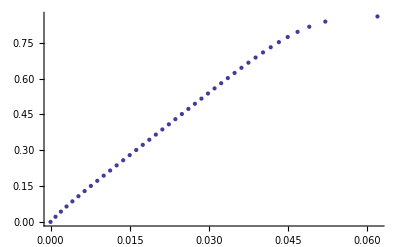

```mathematica
ListPlot[-epssig]
```

```mathematica
EpsSig[proportion_,sigmax_]:=Block[{J2Prop,I1Prop,IJ2,TabEpsp,AllDeriv,FirstDeform,epssig},

J2Prop=Simplify[Sqrt[J2Sig]/.{sig2->sig1 proportion,sig3->sig1 proportion},Assumptions->{sig1<0,propfac>0,propfac<1}];
I1Prop=I1Sig/.{sig2->sig1 proportion,sig3->sig1 proportion};
IJ2=Table[{I1Prop,J2Prop,sig1},{sig1,0,-sigmax,-sigmax/40}];
TabEpsp=IJ2AdjustEpsp[IJ2];
AllDeriv=Table[Derivatives[IJ2[[i]],IJ2[[2]],TabEpsp[[i]]],{i,1,Length[IJ2]}];
FirstDeform={{{0,0},{0,0},0}};
For[i=1,i<Length[AllDeriv],i++,
AppendTo[FirstDeform,FirstDeform[[i]]+(AllDeriv[[i]]+AllDeriv[[i+1]])/2]
];
epssig=Table[{1/3(√3FirstDeform[[i,1,1]]-√2√3 FirstDeform[[i,1,2]]),IJ2[[i,3]]},{i,1,Length[FirstDeform]}];
epssig
]
```

{{0,0.},{-0.00156522,-0.0325},{-0.00315734,-0.065},{-0.00475013,-0.0975},{-0.0063274,-0.13},{-0.0078789,-0.1625},{-0.0093981,-0.195},{-0.0108809,-0.2275},{-0.0123249,-0.26},{-0.0137288,-0.2925},{-0.015092,-0.325},{-0.0164146,-0.3575},{-0.0176971,-0.39},{-0.0189401,-0.4225},{-0.0201447,-0.455},{-0.0213119,-0.4875},{-0.0224429,-0.52},{-0.0235388,-0.5525},{-0.024601,-0.585},{-0.0256307,-0.6175},{-0.0266292,-0.65},{-0.0275977,-0.6825},{-0.0285375,-0.715},{-0.0294498,-0.7475},{-0.0303357,-0.78},{-0.0311965,-0.8125},{-0.0320331,-0.845},{-0.0328467,-0.8775},{-0.0336384,-0.91},{-0.0344091,-0.9425},{-0.0351597,-0.975},{-0.0358913,-1.0075},{-0.0366047,-1.04},{-0.0373007,-1.0725},{-0.0379802,-1.105},{-0.038644,-1.1375},{-0.0392928,-1.17},{-0.0399274,-1.2025},{-0.0405484,-1.235},{-0.0411566,-1.2675},{-0.0417526,-1.3}}

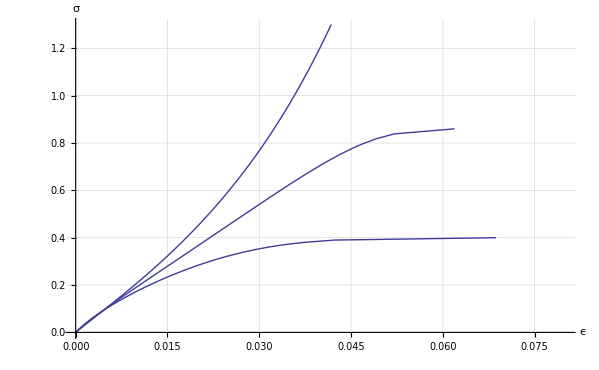

```mathematica
aeps=EpsSig[0.8,1.3]
For[i=1,i≤3,i++,
beps=EpsSig[0.4,0.4]
]
ceps=EpsSig[0.6,0.86];
apl=ListPlot[-aeps,PlotJoined->True];
bpl=ListPlot[-beps,PlotJoined->True];
cpl=ListPlot[-ceps,PlotJoined->True];
Show[cpl,apl,bpl,PlotRange->{{0,0.08},{0,1.3}},AxesLabel->{"ϵ","σ"},GridLines->Automatic]
```

```mathematica
0
```

0